```mathematica
h[x_]:=Piecewise[{{1+Subscript[c, 0,1] x+Subscript[c, 0,2] x^2+Subscript[c, 0,3] x^3, 0≤x≤1}, {Subscript[c, 1,1](x-1)+Subscript[c, 1,2](x-1)^2+Subscript[c, 1,3](x-1)^3, 1<x≤2}, {Subscript[c, 2,1](x-2)+Subscript[c, 2,2](x-2)^2+Subscript[c, 2,3](x-2)^3, 2<x≤3}, {0, True}}];
f[x_]:=h[Abs[x]];
AllVars={Subscript[c, 0,1],Subscript[c, 0,2],Subscript[c, 0,3],Subscript[c, 1,1],Subscript[c, 1,2],Subscript[c, 1,3],Subscript[c, 2,1],Subscript[c, 2,2],Subscript[c, 2,3]};
```

```mathematica
(*Interpolant constraints*)
I1=f[1]
I2=f[2]
I3=f[3]
```

1+c_(0,1)+c_(0,2)+c_(0,3)

c_(1,1)+c_(1,2)+c_(1,3)

c_(2,1)+c_(2,2)+c_(2,3)

```mathematica
(*Partition of unity and linear term*)
T0=CoefficientList[FullSimplify[∑_(k=-2)^3 f[x-k],x>0&&x<1],x]
T1=CoefficientList[FullSimplify[∑_(k=-2)^3 k f[x-k],x>0&&x<1],x]
```

{2+c_(0,1)+c_(0,2)+c_(0,3)+c_(1,1)+c_(1,2)+c_(1,3)+c_(2,1)+c_(2,2)+c_(2,3),-2 c_(0,2)-3 c_(0,3)-2 c_(1,2)-3 c_(1,3)-2 c_(2,2)-3 c_(2,3),2 c_(0,2)+3 c_(0,3)+2 c_(1,2)+3 c_(1,3)+2 c_(2,2)+3 c_(2,3)}

{1+c_(0,1)+c_(0,2)+c_(0,3)+2 c_(1,1)+2 c_(1,2)+2 c_(1,3)+3 c_(2,1)+3 c_(2,2)+3 c_(2,3),-c_(0,1)-2 c_(0,2)-3 c_(0,3)-3 c_(1,1)-4 c_(1,2)-6 c_(1,3)-5 c_(2,1)-6 c_(2,2)-9 c_(2,3),c_(0,2)+3 c_(0,3)+c_(1,2)+6 c_(1,3)+c_(2,2)+9 c_(2,3),-c_(0,3)-3 c_(1,3)-5 c_(2,3)}

```mathematica
GenSols=Solve[{
	I1==0,
	I2==0,
	I3==0,
	T0[[1]]==1,
	T0[[2]]==0,
	T0[[3]]==0,
	T1[[1]]==0,
	T1[[2]]==1,
	T1[[3]]==0,
	T1[[4]]==0
	},
	AllVars
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c_(0,3)→-1-c_(0,1)-c_(0,2),c_(1,3)→-c_(1,1)-c_(1,2),c_(2,1)→-7/5-(7 c_(0,1))/5-(2 c_(0,2))/5-(6 c_(1,1))/5-(c_(1,2))/5,c_(2,2)→6/5+(6 c_(0,1))/5+(c_(0,2))/5+(3 c_(1,1))/5-(2 c_(1,2))/5,c_(2,3)→1/5+(c_(0,1))/5+(c_(0,2))/5+(3 c_(1,1))/5+(3 c_(1,2))/5}}

```mathematica
RegionXY[k_]:={Quotient[k,2],1+Quotient[-k,2]};
Regions=Table[RegionXY[k],{k,-4,7}]
```

{{-2,3},{-2,2},{-1,2},{-1,1},{0,1},{0,0},{1,0},{1,-1},{2,-1},{2,-2},{3,-2},{3,-3}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
φ=1/2;
W[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF=∑_(i=-5)^6 ∑_(j=-5)^6 W[i-j]f[x-i,y-j]/.GenSol;
SimplifySquare[f_,x0_,y0_]:=Simplify[f,x>x0&&x<x0+1&&y>y0&&y<y0+1];
DSimplifySquare[f_,{x0_,y0_}]:=Simplify[D[SimplifySquare[f,x0,y0],{{x,y}}]];
DSumF=ParallelMap[DSimplifySquare[SumF,#]&,Regions];
```

```mathematica
AnisoInt[df_,{x0_,y0_}]:=Simplify[Integrate[Expand[(df.{1,1})^2],{x,x0,x0+1},{y,y0,y0+1}]];
AnisoInts=Parallelize[MapThread[AnisoInt,{DSumF,Regions}]];
Err=Simplify[Total[AnisoInts]]
```

1/63000000(168920343 c_(0,1)^4+2150743 c_(0,2)^4+c_(0,2)^3 (39247427+11652126 c_(1,1)+4020801 c_(1,2))+3 c_(0,1)^3 (338365884+75342324 c_(0,2)+102576067 c_(1,1)+34569742 c_(1,2))+3 c_(0,2)^2 (86246666+9448279 c_(1,1)^2+19003966 c_(1,2)+1129579 c_(1,2)^2+c_(1,1) (53849841+6446208 c_(1,2)))+3 c_(0,1)^2 (37897886 c_(0,2)^2+83257779 c_(1,1)^2+c_(0,2) (342228127+103130826 c_(1,1)+35011901 c_(1,2))+c_(1,1) (472541241+56304408 c_(1,2))+11 (67615656+14850706 c_(1,2)+884389 c_(1,2)^2))+3 c_(0,2) (232270229+11409288 c_(1,1)^3+86575981 c_(1,2)+10688803 c_(1,2)^2+467138 c_(1,2)^3+c_(1,1)^2 (87381503+11614814 c_(1,2))+c_(1,1) (241298906+60310756 c_(1,2)+3997664 c_(1,2)^2))+3 (222162041+11650551 c_(1,1)^4+120694782 c_(1,2)+24785499 c_(1,2)^2+1873308 c_(1,2)^3+162351 c_(1,2)^4+8 c_(1,1)^3 (5500051+1964988 c_(1,2))+c_(1,1)^2 (191553249+45408224 c_(1,2)+8025506 c_(1,2)^2)+c_(1,1) (337003107+134629598 c_(1,2)+15881124 c_(1,2)^2+1843504 c_(1,2)^3))+3 c_(0,1) (681031404+8495924 c_(0,2)^3+34060338 c_(1,1)^3+251022806 c_(1,2)+31195278 c_(1,2)^2+1367488 c_(1,2)^3+24 c_(1,1)^2 (10648647+1439261 c_(1,2))+c_(0,2)^2 (115746802+34626301 c_(1,1)+11844926 c_(1,2))+c_(1,1) (711133281+175897006 c_(1,2)+11824414 c_(1,2)^2)+2 c_(0,2) (252539891+27942204 c_(1,1)^2+55736941 c_(1,2)+3293104 c_(1,2)^2+2 c_(1,1) (79750808+9483079 c_(1,2)))))

```mathematica
FreeVars=Variables[Err];
DErr=Simplify[D[Err,{FreeVars}]];
H=D[DErr,{FreeVars}];
Sols=Solve[DErr==0,FreeVars,Reals];
TableForm[{Range[Length[Sols]],Err/.N[Sols,32],PositiveDefiniteMatrixQ[H/.N[#]]&/@Sols}ᵀ]
```

1 | 0.02955787010686558847340772439 | True

{c_(0,3)→0.1886669181187466540380991161616,c_(1,3)→0.1685945924485987613530168110969,c_(2,1)→0.0925783567627137135531081443433,c_(2,2)→0.0463117823301948740663217655472,c_(2,3)→-0.1388901390929085876194299098905,c_(0,1)→-0.43533022189865716985707333758223,c_(0,2)→-0.75333669622008948418102577857932,c_(1,1)→-0.54806244912683812981019179807705,c_(1,2)→0.37946785667823936845717498698011}

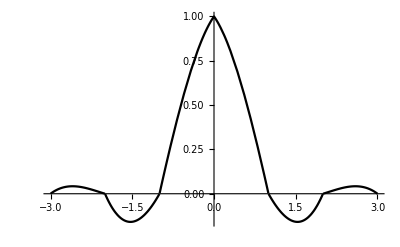

```mathematica
NSol=N[Sols[[1]],32];
FullSol=Join[GenSol/.NSol,NSol]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```